```mathematica
eqn[x_, y_]:=((x^2+2 y^2)^2==x-3x y +y)
```

```mathematica
yprimeEq=D[eqn[x,y[x]],x]
```

2 (x^2+2 y[x]^2) (2 x+4 y[x] y'[x])==1-3 y[x]+y'[x]-3 x y'[x]

```mathematica
sol=Solve[yprimeEq,y'[x]]//Simplify
```

{{y'[x]→(1-4 x^3-3 y[x]-8 x y[x]^2)/(-1+3 x+8 x^2 y[x]+16 y[x]^3)}}

```mathematica
First[sol]
```

{y'[x]→(1-4 x^3-3 y[x]-8 x y[x]^2)/(-1+3 x+8 x^2 y[x]+16 y[x]^3)}

```mathematica
Integrate[x^(-3/2),{x,1,∞}]
```

2

```mathematica
Assuming[t>1, Integrate[x^(-3/2),{x,1,∞}]]
```

2

```mathematica
f[x_]:=2Sin[2x];
```

```mathematica
g[x_]:=x^2;
```

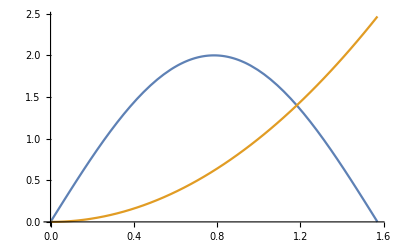

```mathematica
Plot[{f[x],g[x]},{x,0,π/2}]
```

```mathematica
x1=x/.FindRoot[f[x]-g[x],{x,1.2}]
```

1.18315

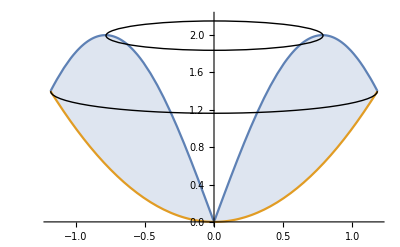

```mathematica
pic = Plot[{f[Abs[x]],g[x]},{x,-x1,x1},Filling-> {1-> {2}},
Epilog-> {Circle[{0,f[x1]},{x1,x1/5},{π,2π}],
Circle[{0,f[π/4]},{π/4,π/20}]},
PlotRange-> {0,2.2}]
```

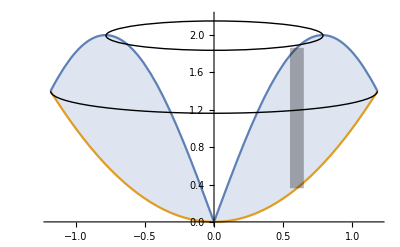

```mathematica
Show[pic,Graphics[{Opacity[.3],Rectangle[{.55,g[0.6]},{.65,f[.6]}]}]]
```

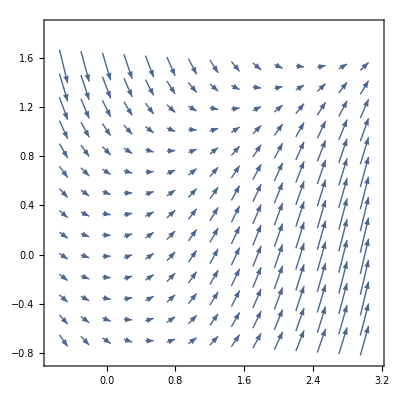

```mathematica
VectorPlot[{1,t-y^2},{t,-0.5,3},{y,-0.7,1.7}]
```